```mathematica
SetDirectory[""];  (*directory of the files*)
```

```mathematica
data=Import["structs6.csv"];
pts=Length[data[[2]]];
ang=360/pts*Pi/180;
c={Circle[{0,0},1]};
Do[c=Append[c,{Disk[{Cos[i*ang],Sin[i*ang]},0.5/pts]}]; c=Append[c,Text[i+1,{Cos[i*ang]+Cos[i*ang]*0.15,Sin[i*ang]+Sin[i*ang]*0.17}]],{i,0,pts-1}]
structs={};
```

```mathematica
Do[x=data[[i]];
 l={c};
 Do[p1=x[[j]]; p2=x[[j+1]];
l=Append[l,Text[i-1,{-1,1}]];
l=Append[l,Line[{{Cos[ang*(p1-1)],Sin[ang*(p1-1)]},{Cos[ang*(p2-1)],Sin[ang*(p2-1)]}}]],{j,1,Length[x]-1,2}];
structs=Append[structs,Graphics[l]],{i,2,Length[data]}]
nn=Divisors[Length[data]-1];
c=4;
Do[If[nn[[i]]≥5,c=nn[[i]]; Break[]],{i,1,Length[nn]}]
```

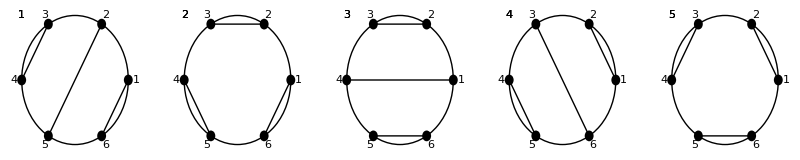

```mathematica
news=ArrayReshape[structs,{Round[(Length[data]-1)/c],c}];
g=GraphicsGrid[news,ImageSize->800]
```

```mathematica
(* in case there are more than 50 structures, separate into different PDFs *)
```

```mathematica
pg=Round[Length[structs]/50]
```

```mathematica
Do[structs1=structs[[i*50+1;;Min[(i+1)*50,Length[structs]]]];news=ArrayReshape[structs1,{Round[(Length[structs1]-1)/5],5}];
g=GraphicsGrid[news,ImageSize->800]; Export["structs_radical"<>ToString[pts-1]<>"p"<>ToString[i+1]<>".pdf",g]
,{i,0,pg}]
```

```mathematica
(* regular single PDF *)
```

```mathematica
Export["structs"<>ToString[pts]<>".pdf",g]
```

structs6.pdf